# NG^4 T_06. Метод опорных векторов: ядра и штрафы

09-март-2023
Шклярик Вера

## 1.Оптимизация вычисления ядра.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train = Import["NG23T06Problem.xlsx", {"Sheets","Шклярик Вера" }]]
```

{4731,3}

```mathematica
Take[Train,3]
```

{{X1,X2,Kind},{1.53717,-1.55497,-1.},{1.82177,1.8957,-1.}}

```mathematica
Map[Dimensions,{X = Rationalize@Train[[2;;,;;2]],Y = Rationalize@Train[[2;;,3]]}]
lenX = Length@X
```

{{4730,2},{4730}}

4730

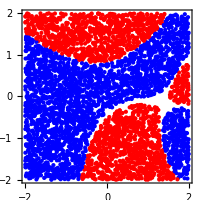

```mathematica
Graphics[{PointSize@Small,{#3/.{-1.->Blue, 1.->Red},Point@{#1,#2}}&@@@Rest@Train},ImageSize->200,Frame->True,AspectRatio->Automatic]
```

```mathematica
Ker1 = (#1.#2+1)^4&;
Ker2 = Compile[{{x1,_Real,1},{x2,_Real,1}},(x1.x2+1)^4];
Ker3 = Compile[{{x1,_Real,1},{x2,_Real,1}},(x1.x2+1)^4,Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
ByteCount/@{Ker1,Ker2,Ker3}
```

{376,2896,3096}

```mathematica
res = ConstantArray[,{3,8}]
```

{{Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null}}

### Function

#### Последовательно

```mathematica
res[[1,2]] = First@Timing[Table[Y[[r]] Y[[c]] Ker1[X[[r]],X[[c]]],{r,lenX},{c,lenX}] ;]
```

70.6719

```mathematica
res[[1,1]] = First@Timing[Table[Yr Yc,{Yr,Y},{Yc,Y}] Table[Ker1[Xr,Xc],{Xr,X},{Xc,X}]  ;]
```

42.2031

```mathematica
res[[1,3]] = First@Timing[Array[Y[[#1]]Y[[#2]]Ker1[X[[#1]],X[[#2]]]&,{lenX,lenX}] ;]
```

94.3281

```mathematica
res[[1,4]] = First@Timing[Outer[Times,Y,Y] Outer[Ker1,X,X,1];]
```

40.2969

#### Параллельно

```mathematica
res[[1,6]] = First@Timing[ParallelTable[Y[[r]] Y[[c]] Ker1[X[[r]],X[[c]]],{r,lenX},{c,lenX}] ;]
```

9.07813

```mathematica
res[[1,5]] = First@Timing[ParallelTable[Yr Yc,{Yr,Y},{Yc,Y}] Table[Ker1[Xr,Xc],{Xr,X},{Xc,X}]  ;]
```

36.375

```mathematica
res[[1,7]] = First@Timing[ParallelArray[Y[[#1]]Y[[#2]]Ker1[X[[#1]],X[[#2]]]&,{lenX,lenX}] ;]
```

5.34375

```mathematica
res[[1,8]] = First@Timing[Parallelize@Outer[Times,Y,Y] Parallelize@Outer[Ker1,X,X,1];]
```

14.0781

### Compile

#### Последовательно

```mathematica
res[[2,2]] = First@Timing[Table[Y[[r]] Y[[c]] Ker2[X[[r]],X[[c]]],{r,lenX},{c,lenX}] ;]
```

55.2344

```mathematica
res[[2,1]] = First@Timing[Table[Yr Yc,{Yr,Y},{Yc,Y}] Table[Ker2[Xr,Xc],{Xr,X},{Xc,X}]  ;]
```

21.1406

```mathematica
res[[2,3]] = First@Timing[Array[Y[[#1]]Y[[#2]]Ker2[X[[#1]],X[[#2]]]&,{lenX,lenX}] ;]
```

67.9063

```mathematica
res[[2,4]] = First@Timing[Outer[Times,Y,Y] Outer[Ker2,X,X,1];]
```

16.4688

#### Параллельно

```mathematica
res[[2,6]] = First@Timing[ParallelTable[Y[[r]] Y[[c]] Ker2[X[[r]],X[[c]]],{r,lenX},{c,lenX}] ;]
```

4.90625

```mathematica
res[[2,5]] = First@Timing[ParallelTable[Yr Yc,{Yr,Y},{Yc,Y}] Table[Ker2[Xr,Xc],{Xr,X},{Xc,X}]  ;]
```

21.6094

```mathematica
res[[2,7]] = First@Timing[ParallelArray[Y[[#1]]Y[[#2]]Ker2[X[[#1]],X[[#2]]]&,{lenX,lenX}] ;]
```

5.95313

```mathematica
res[[2,8]] = First@Timing[Parallelize@Outer[Times,Y,Y] Parallelize@Outer[Ker2,X,X,1];]
```

14.2969

### Compile+

#### Последовательно

```mathematica
res[[3,2]] = First@Timing[Table[Y[[r]] Y[[c]] Ker3[X[[r]],X[[c]]],{r,lenX},{c,lenX}] ;]
```

52.4531

```mathematica
res[[3,1]] = First@Timing[Table[Yr Yc,{Yr,Y},{Yc,Y}] Table[Ker3[Xr,Xc],{Xr,X},{Xc,X}]  ;]
```

21.4844

```mathematica
res[[3,3]] = First@Timing[Array[Y[[#1]]Y[[#2]]Ker3[X[[#1]],X[[#2]]]&,{lenX,lenX}] ;]
```

103.016

```mathematica
res[[3,4]] = First@Timing[Outer[Times,Y,Y] Outer[Ker3,X,X,1];]
```

36.2188

#### Параллельно

```mathematica
res[[3,6]] = First@Timing[ParallelTable[Y[[r]] Y[[c]] Ker3[X[[r]],X[[c]]],{r,lenX},{c,lenX}] ;]
```

10.7813

```mathematica
res[[3,5]] = First@Timing[ParallelTable[Yr Yc,{Yr,Y},{Yc,Y}] Table[Ker3[Xr,Xc],{Xr,X},{Xc,X}]  ;]
```

23.7031

```mathematica
res[[3,7]] = First@Timing[ParallelArray[Y[[#1]]Y[[#2]]Ker3[X[[#1]],X[[#2]]]&,{lenX,lenX}] ;]
```

6.23438

```mathematica
res[[3,8]] = First@Timing[Parallelize@Outer[Times,Y,Y] Parallelize@Outer[Ker3,X,X,1];]
```

14.5781

### Таблица

```mathematica
Grid[res,Frame->All]
```

42.2031 | 70.6719 | 94.3281 | 40.2969 | 36.375 | 9.07813 | 5.34375 | 14.0781
21.1406 | 55.2344 | 67.9063 | 16.4688 | 21.6094 | 4.90625 | 5.95313 | 14.2969
21.4844 | 52.4531 | 103.016 | 36.2188 | 23.7031 | 10.7813 | 6.23438 | 14.5781

```mathematica
SetAccuracy[#,4]&/@res
```

{{42.203,70.672,94.328,40.297,36.375,9.078,5.344,14.078},{21.141,55.234,67.906,16.469,21.609,4.906,5.953,14.297},{21.484,52.453,103.016,36.219,23.703,10.781,6.234,14.578}}

```mathematica
Grid[Join[{{"Матрица","Последовательно",SpanFromLeft,SpanFromLeft,SpanFromLeft,"Параллельно",SpanFromLeft,SpanFromLeft},{SpanFromAbove,"TableEnum", "TableInd","Array","Outer","TableEnum", "TableInd","Array","Outer"}},MapThread[Prepend,{SetAccuracy[#,4]&/@res,{"Function", "Compile","Compile+"}}]],Background->{{Lighter@Lighter@Lighter@Gray},None,{{{1,5},{2,5}}->Lighter@Lighter@Lighter@Lighter@Cyan,{{1,5},{6,9}}->Lighter@Lighter@Lighter@Lighter@Lighter@Blue,{3,4}->Pink,{5,4}->Red,{4,7}->Green,{3,8}->Lighter@Green, {{1,2},{1,1}}->Gray,{{1,2},{2,5}}->Lighter@Lighter@Cyan,{{1,2},{6,9}}->Lighter@Lighter@Lighter@Blue,{{1,1},{2,5}}->Cyan,{{1,1},{6,9}}->Lighter@Lighter@Blue}},Frame->All]
```

Матрица | Последовательно |  |  |  | Параллельно |  |  | 
 | TableEnum | TableInd | Array | Outer | TableEnum | TableInd | Array | Outer
Function | 42.203 | 70.672 | 94.328 | 40.297 | 36.375 | 9.078 | 5.344 | 14.078
Compile | 21.141 | 55.234 | 67.906 | 16.469 | 21.609 | 4.906 | 5.953 | 14.297
Compile+ | 21.484 | 52.453 | 103.016 | 36.219 | 23.703 | 10.781 | 6.234 | 14.578

## 2. Радиально-базисная функция Гаусса в качестве ядра.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train = Import["NG23T06Problem.xlsx", {"Sheets","Шклярик Вера" }]]
```

{4731,3}

```mathematica
Map[Dimensions,{X = Rationalize@Train[[2;;,;;2]],Y = Rationalize@Train[[2;;,3]]}]
lenX = Length@X
```

{{4730,2},{4730}}

4730

```mathematica
Length[iCold = Flatten@Position[Y,-1,1]]
Length[iWarm= Flatten@Position[Y,+1,1]]
```

2767

1963

```mathematica
{lenX,%+%%}
```

{4730,4730}

```mathematica
Fig0 = Graphics[{PointSize@Small,Blue,Point@X[[iCold]],Red,Point@X[[iWarm]]},ImageSize->200,Frame->True,AspectRatio->Automatic]
```

-Graphics-

```mathematica
σ=1;
With[{x= -0.5 σ^-2},Ker = Compile[{{x1,_Real,1},{x2,_Real,1}},Exp[x #.#&[x1-x2]],Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]]
```

CompiledFunction[…]

```mathematica
Plot3D[Ker[{0,0},{x,y}],{x,-2,2},{y,-2,2}, ColorFunction->"GreenPinkTones",PlotRange->All]
```

-Graphics3D-

```mathematica
Timing@Dimensions[Q = ParallelArray[Y[[#1]] Y[[#2]] Ker[X[[#1]],X[[#2]]]&,{lenX,lenX}]]
```

{4.5,{4730,4730}}

```mathematica
iS = RandomSample[Range@lenX,4];
iC = {};
iO = Complement[Range@lenX,iS];
surCharge = 500;
w0 = .234;
Λs = RandomReal[2,4]
```

{1.61627,0.833063,1.6918,1.74846}

SVM(x⃗):=∑_(s∈iS) λ_s y_s Ker(OverVector[x_s],x⃗)+C∑_(c∈iC) y_c Ker(OverVector[x_c],x⃗)-w_0

```mathematica
ClearAll[SVM];
SVM[x_]:=Total@MapThread[#1 #2 Ker[#3,x]&,{Λs, Y[[iS]],X[[iS]]}]+surCharge Total@MapThread[#1 Ker[#2,x]&,{ Y[[iC]],X[[iC]]}]-w0;
```

```mathematica
SVM@{1,-2}
```

0.405405

```mathematica
(*CreatePalette@Dynamic@*)Show[Fig0,ContourPlot[SVM@{x,y},{x,-2.1,2.1},{y,-2.1,2.1},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Directive[Gray,Dashed],Opacity[1,Red]},ContourShading->{Opacity[0.2,Blue],None,Opacity[0.2,Red]}],Graphics[{AbsoluteThickness@3,Green,Circle[#1,Offset@3]&/@X[[iS]],Gray,Circle[#1,Offset@3]&/@X[[iC]]}],ImageSize->200,Frame->False]
```

## 3.Инициализация множества опорных точек.

```mathematica
ClearAll[InitSupport];
InitSupport[counter_]:=With[{iS = Union@Flatten@Table[FixedPoint[(iS = {sCold , sWarm = iWarm[[First@Nearest[X[[iWarm]]->"Index",X[[sCold]],1]]]};iS = {sCold =iCold[[First@Nearest[X[[iCold]]->"Index",X[[sWarm]],1]]], sWarm })&,iS = {sCold = RandomChoice@iCold}],{counter}],iC = {}},{iS, iC,Complement[Range@lenX,iS]}]
```

```mathematica
ClearAll[InitSupport];
InitSupport[counter_]:=Block[{sCold,sWarm},Map[Length,{iS = Union@Flatten@Table[FixedPoint[(iS = {sCold , sWarm = iWarm[[First@Nearest[X[[iWarm]]->"Index",X[[sCold]],1]]]};iS = {sCold =iCold[[First@Nearest[X[[iCold]]->"Index",X[[sWarm]],1]]], sWarm })&,iS = {sCold = RandomChoice@iCold}],{counter}],iC = {},iO = Complement[Range@lenX,iS]}]]
```

```mathematica
InitSupport[5]
```

{10,0,4720}

```mathematica
iS = RandomSample[Range@lenX,4];
iC = {};
iO = Complement[Range@lenX,iS];
surCharge = 500;
w0 = .234;
Λs = RandomReal[2,4]
```

{0.925587,1.15271,1.04467,1.06015}

```mathematica
Step = 0;
CreatePalette[Dynamic[Show[Fig0,ContourPlot[SVM@{x,y},{x,-2.1,2.1},{y,-2.1,2.1},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Directive[Gray,Dashed],Opacity[1,Red]},ContourShading->{Opacity[0.2,Blue],None,Opacity[0.2,Red]}],Graphics[{AbsoluteThickness@3,Green,Circle[#1,Offset@3]&/@X[[iS]],Gray,Circle[#1,Offset@3]&/@X[[iC]]}],ImageSize->200,Frame->False], TrackedSymbols:>{iS,iC}],WindowTitle->Dynamic@ToString@StringForm["Support = ``, Cost = ``, Step = ``",Length@iS, Length@iC,Step]]
```

## 4.Решение задачи квадратичной оптимизации.

{1/2 OverVector[λ_s]·Q_(s,s)·OverVector[λ_s]+𝒞 OverVector[e_c]·Q_(c,s)·OverVector[λ_s]-OverVector[e_s]·OverVector[λ_s]⟶Min
OverVector[y_s]·OverVector[λ_s]+𝒞 OverVector[e_c]·OverVector[y_c]==0

```mathematica
Λ =Table[Subscript[λ, s],{s,iS}]
```

{λ_4537,λ_3798,λ_435,λ_4531}

```mathematica
{0.5 Q[[iS,iS]].Λ.Λ+surCharge Total[Λ.Q[[iS,iC]]]-Total@Λ//Expand,
Y[[iS]].Λ+surCharge Total@Y[[iC]]==0,
Sequence@@Thread[-10<=Λ]}
	Λs = FindArgMin[%,Λ]
```

{-λ_435+0.5 λ_435^2-λ_3798-0.0335212 λ_435 λ_3798+0.5 λ_3798^2-λ_4531-0.0147008 λ_435 λ_4531+0.149278 λ_3798 λ_4531+0.5 λ_4531^2-λ_4537+0.0330163 λ_435 λ_4537-0.0110591 λ_3798 λ_4537-0.364494 λ_4531 λ_4537+0.5 λ_4537^2,λ_435-λ_3798-λ_4531+λ_4537==0,-10≤λ_4537,-10≤λ_3798,-10≤λ_435,-10≤λ_4531}

{1.44588,0.898798,0.931796,1.47888}

w_0:=Median{∑_(i∈iS∪iC) λ_i y_i Ker(OverVector[x_i],OverVector[x_s])-y_s}_(s∈S)

∑_(s∈iS) λ_s y_s Ker(OverVector[x_s],x⃗)+C∑_(c∈iC) y_c Ker(OverVector[x_c],x⃗)

Мои неудачные попытки вычислить w0

```mathematica
(Λs.Q[[iS,1]])/Y[[1]]+Total[surCharge Q[[iC,1]]]/Y[[1]]-Y[[1]]
```

7.63399

```mathematica
(Λs.Q[[iS,iS]])/Y[[iS]]+Total[surCharge Q[[iC,iS]]]/Y[[iS]]-Y[[iS]]
```

{-2.28553,-2.28553,-2.28553,-2.55099,-2.28553,-2.28553}

```mathematica
Λs.Q[[iS,iS]]
surCharge Q[[iC,iS]]
```

{-1.28553,-1.28553,3.28553,3.55099,3.28553,-1.28553}

{}

```mathematica
w0 = Median[MapIndexed[(Λs.Q[[iS,First@#2]])/#1+Total[surCharge Q[[iC,First@#2]]]/#1-#1&,Y]]
```

3.25211

```mathematica
iS//Length
```

6

```mathematica
Λ.Q[[iS,iC]]
```

{}

Удачная попытка вычислить w0

```mathematica
w0 = Median[SVM/@X[[iS]]-Y[[iS]]]
```

0.766

```mathematica
Λ = Table[Subscript[λ, s],{s,iS}]
```

{λ_4537,λ_3798,λ_435,λ_4531}

```mathematica
w0 = 0;
 Median[SVM/@X[[iS]]-Y[[iS]]]
```

-2.58024

```mathematica
ClearAll[SolveQP];
w0 = 0;
SolveQP[iS_,iC_,surCharge_]:=With[{Λ = Table[Subscript[λ, s],{s,iS}]},{Λs = FindArgMin[{0.5 Q[[iS,iS]].Λ.Λ+surCharge Total[Λ.Q[[iS,iC]]]-Total@Λ//Expand,
Y[[iS]].Λ+surCharge Total@Y[[iC]]==0,
Sequence@@Thread[-10<=Λ]},Λ], Median[SVM/@X[[iS]]-Y[[iS]]]}]
```

```mathematica
InitSupport[10];
{Λs,w0}=SolveQP[iS,iC,surCharge]
```

{{-10.,-10.,112.392,115.887,214.787,-9.29838,1254.27,345.924,31.7665,-10.,224.564,-10.,-10.,343.289,12.9757,1220.27},2.38719}

1. Сгенерировали 20 опорных точек и построили разделительную полосу.
-Graphics-
□

## 5. Опорные точки и точки-нарушители.

```mathematica
iS
```

{613,855,1073,1511,2184,2199,2745,2813,3147,3181,3253,3840,4256,4454,4543,4709}

```mathematica
Λs
```

{-10.,-10.,112.392,115.887,214.787,-9.29838,1254.27,345.924,31.7665,-10.,224.564,-10.,-10.,343.289,12.9757,1220.27}

```mathematica
Length[mO = SVM/@X[[iO]]];
Min@mO
Position[mO,%,1,1]
iC = Extract[iO,%]
```

-32.3306

{{2461}}

{2467}

2. Нашли первую точку-нарушителя (внутреннюю точку с неправильными отступами)
-Graphics-

```mathematica
Min@Λs
If[%<0, iC =Flatten@Append[iC ,Extract[iS,Position[Λs,%,1,1]]],"Ok"]
```

-10.

{2467,3840}

3. Нашли вторую точку-нарушителя (опорную точку с неправильными значениями коэффициентов Лагранжа)
-Graphics-

```mathematica
Append[iO,Last@iC];
Append[ iS,First@iC];
iC = {};
Step+=1;
SolveQP[iS,iC,surCharge];
```

4. Скорректировали положение разделительной полосы.
-Graphics-